## Mathematica dealing with rho from matlab

### Importing cr, cf, and cl1 from Mat bt matlab

```mathematica
CC500dim3=Import["E:\\06_Coh\\00_Code\\00_dim3gs\\00_data\\a0_20191008_cc_10000.mat"];purity500dim3=Import["E:\\06_Coh\\00_Code\\00_dim3gs\\00_data\\a0_20191008_purity_10000.mat"];
CCdim3a=Flatten[CC500dim3,1];
CCdim3=Flatten[CCdim3a,2];
Dimensions[Flatten[CCdim3,1]]
puritydim3a=Flatten[purity500dim3,1];
puritydim3=Flatten[puritydim3a,2];
Dimensions[Flatten[puritydim3,1]]
```

{10000}

{10000}

#### CR versus Cl1

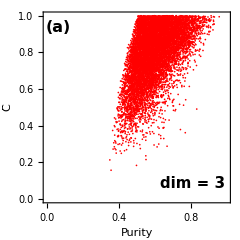

```mathematica
dim =3;
clcrd3=Transpose[{puritydim3,CCdim3}];
fig001d3=ListPlot[clcrd3,PlotRange->{{0,1.},{0,1.}},Frame->True,FrameStyle->{{Thick,Thick},{Thick,Thick}},PlotStyle->{{Red,Thick,PointSize[0.005]}},LabelStyle->{15,Bold},FrameLabel->{Style["Purity",FontSize->16],Style["C̄",FontSize->16]},FrameTicksStyle->Directive[12.5],Epilog->{Text[Style["(a)",FontSize->16,FontWeight->"Bold"],Scaled[{.08,.92}]],Text[Style["dim = 3",FontSize->15,FontWeight->"Bold"],Scaled[{.8,.1}]](*,Text[Style["y = (x+1)/3",FontSize->18,FontWeight->"Bold"],Scaled[{.7,.85}]]*)},ImageSize->{240,240},AspectRatio->1,GridLines->{{1/dim},None},GridLinesStyle->Directive[Blue,Dashed]]
(*fig002d3=Plot[{x},{x,0,1.05},PlotRange->{{0,1.05},{0,1.05}},PlotStyle->{{Thickness[0.005],Darker[Green],Dashed}}];(* d1 is dim *)
figdim3=Show[fig001d3,fig002d3]*)
```